```mathematica
n1=1;"$ player";
n2=1;"MG player";
n3=99;"Back ground";
n=n1+n2+n3;
m=2;
P=2^m;
T=400-1;"odd steps needs";
mu=Table[0,{i,1,T}];
normalize=1/(√n);
S=2;
t=3;
mu⟦1⟧=RandomInteger[P-1];
mu⟦2⟧=RandomInteger[P-1];
signal=0;
"bestStrategy⟦i⟧,U⟦i,s⟧";"Side⟦i,bestStrategy⟦i⟧,mu⟧-->From book";
"StategySpace-->we don't construck it";
"Action=List[IntegerDigits[StrategyPosition=RandomInteger[{0,2^(2^m)-1}],2,4]]";
"AgentStrategy⟦i,s⟧--> i^thagents and the s^th strategy";
PayoffFunction=Table[0,{i,1,n},{s,1,S}];
A=Table[0,{i,1,T}];
nM=Table[0,{i,1,T}];
ΔcM=Table[0,{i,1,T}];
bestStrategy=Table[0,{i,1,n},{j,1,2}];"bestStrategy⟦Fresh,React⟧";
BS=Table[0,{i,1,n},{j,1,2}];
U=Table[1,{i,1,n},{i,1,S}];
Price=Table[0,{i,1,T}];
Price⟦2⟧=Price⟦1⟧=10;"Resource level {C_i(0),n_i(0)}={n*p(0),n-1},n=10";
W=Table[190,{i,1,n}];
c=Table[100,{i,1,n}];
NStock=Table[9,{i,1,n},{i,1,2}];
AgentStrategy=Table[0,{i,1,n},{i,1,S}];
Tinfor=Table[0,{i,1,P}];
Onetimes=Table[0,{i,1,P}];
CondionPinfor=Table[0,{i,1,P}];
BScollect=Table[0,{i,1,n}];
"initial set";
Do[
Action=List[IntegerDigits[StrategyPosition=RandomInteger[{0,2^P-1}],2,P]];
Do[Action⟦1,k⟧=(2*Action⟦1,k⟧-1),{k,1,P}];
RandomStrategy=Action;
AgentStrategy⟦i,s⟧=Flatten[RandomStrategy,1],{s,1,S},{i,1,n}]
Do[AgentStrategy⟦i,s⟧=AgentStrategy⟦1,s⟧,{s,1,S},{i,2,n1+n2}];
Do[bestStrategy⟦i,1⟧=RandomChoice[Select[Table[If[U⟦i,s⟧≥Max[U⟦i⟧],AgentStrategy⟦i,s⟧],{s,1,S}],ListQ]],{i,1,n}];
Do[bestStrategy⟦i,2⟧=bestStrategy⟦i,1⟧,{i,1,n}];
Do[BS⟦i,1⟧=Table[-bestStrategy⟦i,2⟧⟦mu⟦t-1⟧+1⟧,{k,1,P}],{i,1,n1}];
Do[BS⟦i,1⟧=bestStrategy⟦i,1⟧,{i,n1,n}];
```

```mathematica
(Label[begin];
"Nature choice";
mu⟦t⟧=RandomInteger[P-1];
"mu⟦t⟧=Mod[2*mu⟦t-1⟧+signal,P]";
"group I,II  Agents choice s_i^*(t)=argmax{U_(i, s)(t)}  ,sent order";
Do[bestStrategy⟦i,2⟧=bestStrategy⟦i,1⟧,{i,1,n}];
Do[BS⟦i,2⟧=BS⟦i,1⟧,{i,1,n}];
Do[bestStrategy⟦i,1⟧=RandomChoice[Select[Table[If[U⟦i,s⟧≥Max[U⟦i⟧],AgentStrategy⟦i,s⟧],{s,1,S}],ListQ]],{i,1,n}];
If[OddQ[t],Do[BS⟦i,1⟧=bestStrategy⟦i,1⟧,{i,1,n1}];
Do[If[BS⟦i,1⟧==AgentStrategy⟦i,1⟧,BScollect⟦i⟧=BScollect⟦i⟧+1,BScollect⟦i⟧=BScollect⟦i⟧-1],{i,1,n1}];,
Do[BS⟦i,1⟧=Table[-bestStrategy⟦i,2⟧⟦mu⟦t-1⟧+1⟧,{k,1,P}],{i,1,n1}]];
Do[BS⟦i,1⟧=bestStrategy⟦i,1⟧,{i,n1+1,n}];
"Market interaction A(t)=Σ_(i = 1)^na_(i, s*)(t)
Market Maker n_M(t)=-Σ_(t = 3)^(t - 1)A(t)";
MarketAction=0;
Do[MarketAction=MarketAction+BS⟦i,1⟧⟦mu⟦t⟧+1⟧,{i,1,n}];
A⟦t⟧=MarketAction;
nM⟦t⟧=(nM⟦t-1⟧+(-A⟦t-1⟧));
"signal=UnitStep[MarketAction]";
"Price/Cash/Wealth update deal t+1 ";
Price⟦t⟧=Price⟦t-1⟧+normalize*(A⟦t-1⟧);
If[t==3,Do[c⟦i⟧=100,{i,1,n}];
Do[NStock⟦i,2⟧=9,{i,1,n}];Do[W⟦i⟧=190,{i,1,n}];,Do[c⟦i⟧=c⟦i⟧-BS⟦i,2⟧⟦mu⟦t-1⟧+1⟧(Price⟦t⟧);
c⟦i⟧=N[c⟦i⟧],{i,1,n}];
Do[NStock⟦i,1⟧=NStock⟦i,2⟧;
NStock⟦i,2⟧=NStock⟦i,1⟧+BS⟦i,2⟧⟦mu⟦t-1⟧+1⟧,{i,1,n}];
Do[W⟦i⟧=W⟦i⟧+NStock⟦i,1⟧*(Price⟦t⟧-Price⟦t-1⟧);
W⟦i⟧=N[W⟦i⟧],{i,1,n}];];
ΔcM⟦t⟧=+A⟦t-1⟧*Price⟦t⟧;
"Agents learning Payoff g_(i, s)(t)=0,odd,g_(i, s)(t)=a_(i, s)(t-1)A(t),even g_(i, s)(t)=-a_(i, s)(t)A(t)";
If[OddQ[t],Do[PayoffFunction⟦i,s⟧=0,{s,1,S},{i,1,n1}];,
Do[PayoffFunction⟦i,s⟧=(AgentStrategy⟦i,s⟧⟦mu⟦t-1⟧+1⟧)(A⟦t⟧),{s,1,S},{i,1,n1}];]
Do[PayoffFunction⟦i,s⟧=-(AgentStrategy⟦i,s⟧⟦mu⟦t⟧+1⟧)(A⟦t⟧),{s,1,S},{i,n1+1,n}];
Do[U⟦i,s⟧=U⟦i,s⟧+PayoffFunction⟦i,s⟧,{s,1,S},{i,1,n}];
t=t+1;
"Go on or Stop";
If[t>T,Break,Goto[begin]];)//AbsoluteTiming
```

{3.16818,Null}

```mathematica
A
N[-ΔcM,4]
N[Table[A⟦i⟧*Price⟦i+1⟧,{i,3,8}],4]
```

{0,0,5,-61,9,-5,7,-11,-21,43,41,-1,31,9,-31,-9,31,-31,31,-57,41,5,7,-39,45,-39,-13,-45,31,-29,-1,27,3,-5,29,37,-37,-21,-19,11,43,1,-25,41,-33,-11,11,-11,13,-45,33,23,49,-21,-47,3,39,-39,23,-23,-9,11,-11,-29,45,13,-59,43,23,-15,23,-37,-35,-15,25,25,-19,-19,17,43,-23,27,-21,-39,43,7,-47,-1,51,17,-13,25,-5,3,-47,49,11,-11,-47,49,11,-33,-1,-47,41,-57,-3,45,-39,-3,1,45,-45,43,-43,1,1,1,-3,45,-21,41,-23,29,1,9,-21,-47,13,19,-3,43,-25,13,27,-33,31,-25,-17,31,-1,-37,-21,15,-27,43,-59,27,-11,45,-47,49,-19,9,25,-49,11,-33,31,-11,7,-35,-5,3,-1,37,1,3,-25,-5,45,-5,7,-11,33,-45,41,-39,13,-37,-21,27,33,27,-39,25,-27,37,-37,39,-17,-35,19,23,-39,45,17,-47,61,1,-1,-1,-21,1,-21,5,7,9,-7,-7,7,-11,-1,7,7,19,-3,-5,-9,-9,11,1,3,-29,-11,-1,1,-45,21,41,11,-39,-23,53,-47,25,-15,-37,13,23,39,-13,-49,39,31,-3,-1,-37,15,-21,15,-13,45,-15,-23,21,-21,-45,5,3,21,45,31,-49,1,-11,45,-27,-41,45,35,1,-33,-41,41,-33,-9,31,-33,17,29,-27,45,-19,21,-61,-11,11,-23,27,43,-39,59,15,-37,7,-3,-47,-15,-15,11,37,39,-47,-31,13,45,-53,39,-13,-11,-9,-15,45,33,15,-23,33,-11,-59,47,-37,9,-13,3,-7,-19,-15,9,1,13,43,-19,-19,27,-31,15,-23,-29,19,37,35,-17,-37,21,-25,33,-33,-27,23,-19,33,-37,39,35,13,-13,-39,23,-25,39,-39,-29,27,27,5,3,29,-25,-9,-25,15,-39,23,47,-19,15,-47,-17,31,53,-37,-21,-37,27,43,23,7,-23,-35,-11,-37,31,25,35,11,-43,-27,-19}

{0,0,0,-52.49,270.1,-47.91,24.13,-38.66,48.71,49.1,-284.5,-438.6,10.6,-424.1,-131.2,356.3,95.37,-424.1,328.5,-424.1,456.6,-495.7,-62.94,-92.99,366.7,-624.6,390.,113.2,190.3,-226.7,128.4,4.328,-189.4,-21.94,34.08,-281.3,-495.2,359.,159.9,108.7,-74.97,-477.1,-11.19,217.7,-524.2,313.6,92.49,-104.5,92.49,-126.1,235.1,-280.7,-248.3,-767.9,285.2,418.6,-27.61,-510.3,359.,-264.3,211.7,74.78,-103.4,91.39,157.3,-445.5,-145.5,314.1,-412.9,-273.5,156.,-291.8,333.2,193.3,60.45,-162.9,-225.1,135.2,99.25,-117.6,-481.3,204.8,-313.,199.6,219.3,-425.7,-74.18,278.3,5.821,-555.7,-214.,146.8,-344.5,66.42,-40.75,418.6,-675.3,-163.6,151.6,427.9,-685.,-165.8,389.1,11.69,329.7,-454.9,309.1,15.37,-432.1,223.1,16.27,-5.522,-450.,248.5,-421.4,237.5,-5.622,-5.721,-5.821,16.57,-450.,166.1,-491.6,223.1,-365.,-12.69,-122.2,241.3,320.3,-105.4,-190.,29.1,-601.1,287.3,-166.2,-417.8,402.2,-473.5,319.7,188.6,-439.6,14.08,384.7,174.5,-147.,192.1,-489.9,325.8,-221.6,78.26,-521.6,325.,-577.8,188.1,-97.16,-332.1,412.,-104.5,205.2,-288.4,90.3,-62.34,189.8,24.63,-15.67,5.124,-325.8,-8.905,-27.61,167.9,31.09,-481.3,51.,-76.27,107.8,-431.8,387.3,-520.2,343.4,-131.3,237.5,90.89,-189.4,-339.9,-350.6,355.1,-289.8,240.4,-465.7,329.5,-498.7,188.6,266.4,-180.5,-271.2,308.5,-557.5,-239.4,441.9,-943.8,-15.57,15.47,15.37,279.,-13.38,237.2,-58.96,-87.41,-120.4,88.81,83.93,-88.81,127.5,11.49,-85.32,-90.2,-280.7,43.43,69.9,117.8,109.7,-146.1,-13.38,-41.04,313.1,106.7,9.602,-9.701,235.1,-153.6,-467.1,-137.4,335.7,145.3,-614.4,325.,-235.1,118.7,156.5,-71.79,-179.7,-456.,135.2,270.6,-366.7,-387.1,36.57,12.09,311.1,-148.5,164.,-139.6,104.1,-561.9,164.9,200.2,-226.7,182.8,190.3,-23.63,-15.07,-149.4,-521.6,-455.,480.2,-9.9,96.87,-597.8,286.1,267.2,-494.8,-506.7,-14.58,372.7,295.8,-463.,264.3,64.03,-316.2,228.2,-146.3,-333.3,237.8,-597.8,216.5,-283.1,452.2,69.5,-81.54,117.9,-210.9,-519.9,320.1,-830.7,-233.6,440.,-88.11,36.87,357.8,91.79,69.4,-62.93,-347.9,-518.1,404.5,171.2,-88.61,-508.2,319.1,-386.1,111.9,82.64,59.55,76.86,-432.1,-425.2,-215.7,278.1,-507.3,157.1,496.1,-615.,347.9,-92.69,117.1,-27.91,60.25,127.6,78.36,-55.07,-6.219,-97.66,-507.,188.1,152.2,-288.8,236.,-136.6,156.8,114.,-110.6,-351.6,-454.5,192.,281.6,-203.7,180.3,-346.4,238.1,122.2,-156.8,93.58,-270.9,167.5,-327.9,-416.2,-171.4,154.6,312.4,-236.9,195.3,-456.,304.6,142.8,-205.5,-278.1,-53.98,-33.28,-405.4,287.3,95.37,202.7,-144.,223.1,-184.2,-596.3,205.1,-184.3,357.8,100.6,-279.2,-756.8,392.1,178.7,178.6,-202.8,-507.,-323.8,-103.4,287.2,315.2,87.01,156.5,-226.7,-245.,-464.9,-158.2,434.3,200.1}

{52.49,-270.1,47.91,-24.13,38.66,-48.71}

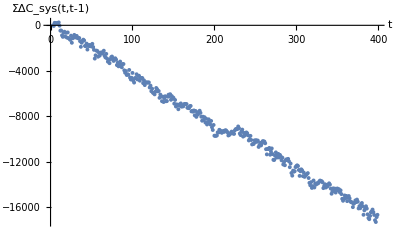

```mathematica
ListPlot[Table[{t,N[Total[-ΔcM⟦1;;t⟧]]},{t,3,T}],PlotStyle->PointSize[0.007],AxesLabel->{"t","ΣΔC_sys(t,t-1)"},LabelStyle-> {10,FontFamily->"Times New Roman",GrayLevel[0],Italic}]
```

```mathematica
nM
N[Price,4]
```

{0,0,0,-7,-6,47,30,35,60}

{10.,10.,10.,10.7,10.6,5.323,7.015,6.517,4.03}

```mathematica
N[Table[-nM⟦i⟧*Price⟦i+1⟧,{i,3,8}],4]
```

{0,74.18,31.94,-329.7,-195.5,-141.}

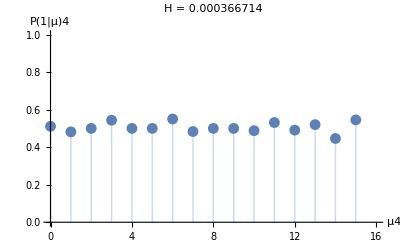

```mathematica
"P(1|μ4),P(1|μ6)";
Do[Tinfor⟦μ⟧=Tinfor⟦μ⟧+KroneckerDelta[mu⟦t⟧,μ-1];
Onetimes⟦μ⟧=Onetimes⟦μ⟧+UnitStep[A⟦t⟧]*KroneckerDelta[mu⟦t⟧,μ-1];,{t,Floor[T/2],T},{μ,1,P}];
"Tinfor";
Do[CondionPinfor⟦μ⟧=Onetimes⟦μ⟧/Tinfor⟦μ⟧,{μ,1,P}];
"prediction  H=Σ_(μ = 0)^(P - 1)ρ^μ<A|μ>^2,ρ^μ=T_μ/T";
Aonμ=0;
H=0;
Do[Do[Aonμ=Aonμ+A⟦t⟧*KroneckerDelta[mu⟦t⟧,μ-1],{t,Floor[T/2],T}];
Aonμ=Aonμ/Tinfor⟦μ⟧;
H=H+Tinfor⟦μ⟧/(T/2)*(Aonμ)^2;,{μ,1,P}]
f0=ListPlot[Table[{μ-1,CondionPinfor⟦μ⟧},{μ,1,P}],Filling
->Axis,PlotRange->{{0,P},{0,1}},AxesLabel-> {"μ"<>ToString[m],"P(1|μ)"<>ToString[m]},PlotLabel->"H = "<>ToString[N[H/n]]]
```

```mathematica
Q=1/n Sum[(2/T*BScollect⟦i⟧)^2,{i,1,n}]//N
```

0.438852

```mathematica
"Anylize   P(t+1)-P(t)=r(t)=(A (t))/λ   P(0)=10";
```

```mathematica
N[Variance[A]]
```

55.9457

```mathematica
1/(n*T)Sum[(A⟦i⟧-(Mean[A]))^2,{i,1,T}]//N
```

0.553572

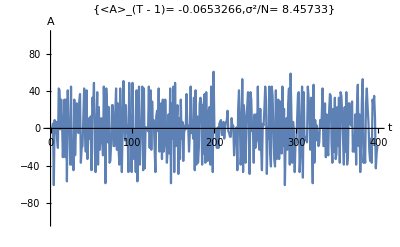

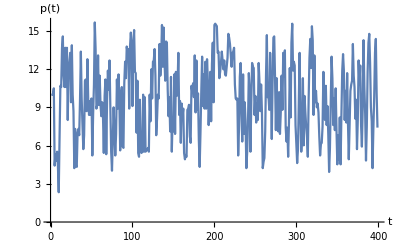

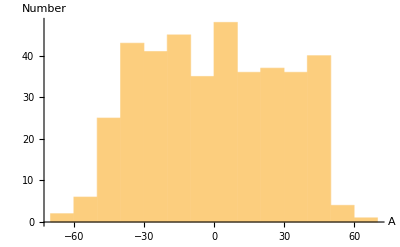

```mathematica
t1=0;
t2=T;
f1=ListPlot[A,AxesLabel->{"t","A"},PlotRange->{{t1,t2},{-n,n}},Joined->True,PlotLabel->{"<A>_(T - 1)= "<>ToString[N[Mean[A⟦t1+1;;t2-1⟧]]],"σ^2/N= "<>ToString[N[1/n Variance[A]]]}]
f2=ListPlot[Price⟦t1+1;;t2⟧,AxesLabel->{"t","p(t)"},PlotRange->Automatic,Joined->True,LabelStyle-> {14,FontFamily->"Times New Roman",GrayLevel[0],Italic}]
f3=Histogram[A⟦t1+1;;t2⟧,AxesLabel->{"A","Number"}]
```

```mathematica
1/(n*T)Sum[(A⟦i⟧)^2,{i,1,n}]//N
```

0.465607

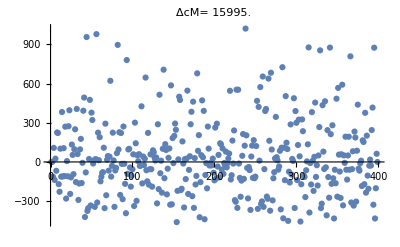

```mathematica
ListPlot[ΔcM,PlotLabel-> "ΔcM= "<>ToString[N[Total[ΔcM⟦1;;T⟧]]]]
```

```mathematica
-Total[ΔcM⟦1;;T⟧]+(9n-nM⟦T⟧)*Price⟦T⟧-(9n*Price⟦1⟧)//N
```

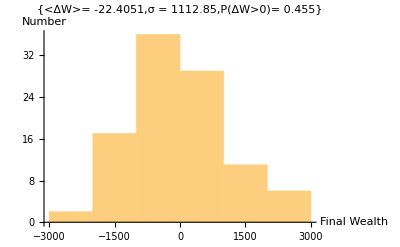

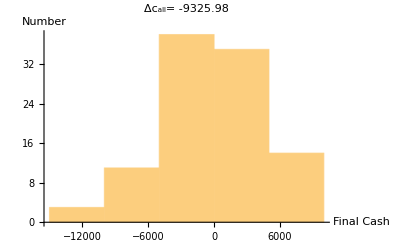

```mathematica
f4=Histogram[W⟦1;;n⟧-190,Automatic,AxesLabel->{"Final Wealth","Number"},PlotLabel->{ "<ΔW>= "<>ToString[N[Mean[W-190]]],"σ = "<>ToString[N[StandardDeviation[W-190]]],"P(ΔW>0)= "<>ToString[N[1/n Total[UnitStep[W-190]],3]]}]
f5=Histogram[c⟦1;;n⟧-100,Automatic,AxesLabel->{"Final Cash","Number"},PlotLabel-> "Δc_all= "<>ToString[N[Total[c⟦1;;n⟧-100]]]]
```

```mathematica
Sum[A⟦t⟧*Price⟦t⟧,{t,1,T}]//N
Sum[1/(√n)(A⟦t⟧)^2,{t,1,T}]//N
```

11221.4

5728.73

```mathematica
c
```

{-117.913,2742.89,-6467.88,507.166,-15793.9,-7877.01,2937.71,12886.8,16011.4,5602.37,-2623.22,13986.4,8147.35,-585.691,-15287.1,-10469.4,7017.31,11421.5,-3769.09,-1811.38,-15420.,-13.6204,-12353.,-4512.65,-15424.3,-1994.65,-12016.4,-13632.5,3716.09,10951.5,7743.28,7701.99,4525.05,4759.5,-12894.1,10824.7,-8774.24,13832.5,-12025.,22391.8,7784.61,7711.14,-1155.05,3723.66,-4565.58,5531.06,12931.2,12880.6,6209.06,-12902.7,-12179.5,65.8824,-8060.59,-6415.14,-11475.,14451.6,8774.72,-16664.1,1988.24,-7848.19,-7736.45,-5882.2,8294.03,702.29,4445.94,-12353.,-6144.4,-9079.44,-15455.4,11760.8,-7721.12,16191.8,-6664.5,-11517.2,-10866.5,22351.9,485.469,-6436.84,-6529.36,10912.,-6418.1,-3852.37,-11626.9,-5141.01,-1659.12,6960.28,4652.83,-9069.69,6844.47,14452.5,-16676.,-11381.2,-2028.88,-11958.1,507.166,-4742.42,-8723.7,-15356.6,-926.169,14451.6,14442.8}